### Categorization

Tutorial

Indivaria

Indivaria`

Indivaria/tutorial/1012

### Keywords

Details

# Model 1.0-1.2

Model 1.0 to 1.2 are the models for studying the malaria parasite (p. falciparum) dynamics in a patient during treatment with artesunate (artemisinin derivative). The models are based on White's model (model 1.4) and Hoshen's model (model 1.3). These models assume that the age distribution of parasites in a patient on admission follows a normal distribution with a mean μ hours and a standard deviation σ hours. The parasites in the patient are assumed to have the same life-cycle and the same parasite multiplication rate (PMR). The models devide the parasite ages into three sensitive groups (start from the asexual stage Rings to Schizonts). Each sensitive group has its own concentration-effect relationship.

The models were used in the study of artemisinin resistance. For more details of the models and results, see Saralamba S., et al., Intrahost modeling of artemisinin resistance in Plasmodium falciparum, PNAS (2011). Diagram below illustrating the model structure, its inputs, and its outputs. An initial population of parasites (Left) is distributed normally over age and moves to the right over time. The concentration of the drug over time (Center) is incorporated into the model by assuming that subsequent doses have the same concentration profile as the initial measured dose for each patient. The model then combines a dose–effect relationship with the drug concentration to determine how many parasites at each stage are killed by the drug at each time point. The total number of circulating parasites predicted by the model is fitted to the observed parasite density data (Center) and the resistance index for each stage is inferred from the dose–effect curve (Right).

-Graphics-

## Model 1.0

Model 1.0 generates modeled parasite count data during treatment with artesunate. It requires the pharmacokinetic data (DHA concentration). The user must input the values of parameters related to the efficacy of artesunate (pharmacodynamic parameters) for each sensitive stage such as emin, emax, ec50 and gamma.

parameter names | descriptions
model | model ID
initn | initial load of parasites
lifecycle | parasite life-cycle (hours)
mu | the mean age of parasites on admission (hours)
sigma | the standard deviation of parasites on admission (hours)
pmr | parasite multiplication rate (per life-cycle)
everyh | duration between each dose of artesunate (hours)
ndrug | number of doses 
concfile | the file name of DHA concentration data
killzone | the ranges of the ages of parasites that sensitive to artesunate
gamma | constants related to the slope of EC curve 
ec50 | 50% efficacy concentration
emin | minimum efficacy
emax | maximum efficacy
1/alpha | model constant
runmax | maximum runtime of the model (hours)
lim | the number of parasite at the detection limit (in log10)
outform | the output form

List of parameters of model 1.0.

Model 1.0 has four output form. See table below.

0 | show the number of parasites at each age (1-life-cycle (hours)) over time.
1 | write log10(total number of parasites) of every time step (hour) to "modgen.csv".
2 | show log10(total number of parasites) of every time step (hour).
3 | show parasite reduction ratio at 24 and 48 hours (if runmax > 48), parasite clearance time, minimum parasite and recrudescence time (if exist).

Values of outform for model 1.0.

This is an example of the input file for model 1.0. Here the patient receives artesunate every 24 hours for 7 times. The initial load of parasites is 2.3*10^11 with the mean age 10 hours and SD 5 hours. All parasites have the multiplication rate about 10. The DHA concentration data is in the file "P002.csv". The sensitive ages of parasites are divided into three groups: Rings 6-26, Trophozoites 27-38 and Schizonts 39-44. Each group has its own efficacy-concentration curve (EC curve). The value of parameters for this EC curve are as given. The number of parasites at the detection limit is 10^8.

# the example of the input file for the model 1.0
model 1.0

initN	2.30*10^11	# initial number of parasites
lifecycle	48		# the life cycle of parasites 
mu	10	# mean age of parasites on admission
sigma	5	# SD of the age of parasites  
pmr 10  # parasite multiplication rate

everyH   24 # duration (hours) of giving the drug
Ndrug 	7	# number of the drug

Concfile 	"P002.csv"  # the name of DHA concentration file	

KillZone 	{{6, 26}, {27, 38}, {39, 44}}	# the ranges of the age of sensitive parasites
gamma	{5.5, 5.5, 5.5}		# the slopes of the EC curves
ec50	{20.0, 20.0, 20.0}	# the EC50 for each kill zone
emin 	{0.0, 0.0, 0.0}		# minimum efficacy of the drug
emax 	{99.99, 99.99, 99.99} 	# maximum efficacy of the drug
1/alpha		5.5			# the action time (hours) 

runMax	100  # maximum runtime

lim		8.0		# the detection limit (in log10 scale)

outform	0 # output forms

The result from above input.

```mathematica
ls =IDVL["mod1_0.in"];
```

******INDIVARIA*****

model: 1.

outform: 0

********************

model: 1.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

outform: 0

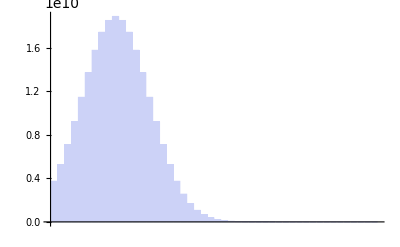
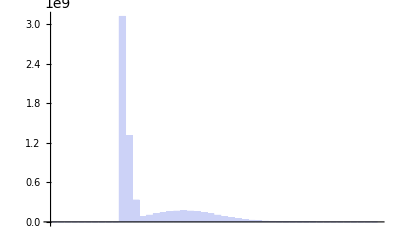
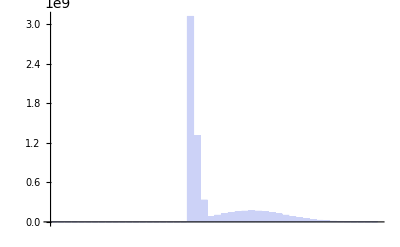
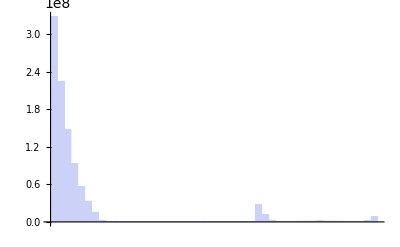
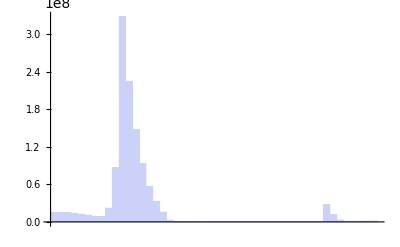
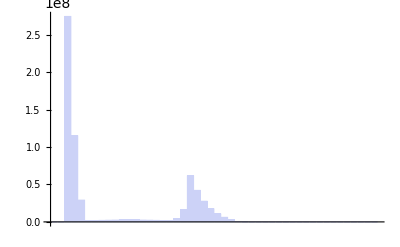
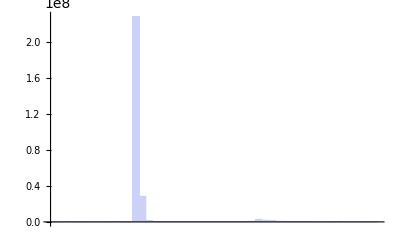
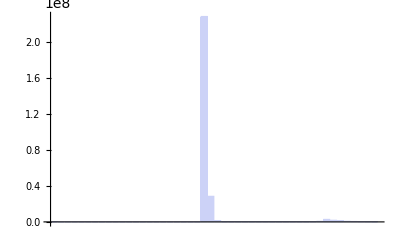

```mathematica
Table[BarChart[ls[[i]]],{i,1,Length@ls,10}]
```

This the result when outform is 2.

```mathematica
ls =IDVL["mod1_0.in"];
```

******INDIVARIA*****

model: 1.

outform: 2

********************

model: 1.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

runmax: 100

outform: 2

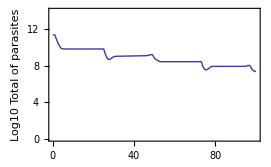

```mathematica
ListPlot[ls,PlotRange->{0,14},Joined->True,Frame->True,FrameLabel->{"time(hours)","Log10 Total of parasites"}]
```

The result of outform = 3

```mathematica
IDVL["mod1_0.in"]
```

******INDIVARIA*****

model: 1.

outform: 3

********************

model: 1.

initn: 2.30*10^11

pmr: 10

mu: 10

sigma: 5

lifecycle: 48

killzone: {{6,26},{27,38},{39,44}}

concfile: P002.csv

everyh: 24

ndrug: 7

gamma: {5.5,5.5,5.5}

ec50: {20.0,20.0,20.0}

emin: {0.0,0.0,0.0}

emax: {99.99,99.99,99.99}

1/alpha: 5.5

lim: 8.

outform: 3

Total time: 240

intersection: {{62},{239}}

prr24: 764.308

prr48: 251.097

clearance time: 66

pmin(log10): 4.75107

recrudescence time: 240

{240,{{62},{239}},764.308,251.097,66,4.75107,240}

Example of DHA concentration data. Time and the concentration is separated by comma.

0, 0.1
0.25, 25.5
0.5, 515
1, 644
1.5, 387
2, 204
3, 55.7
4.12, 13.7
5.08, 10.9
6, 5.36
8, 2.09
11.83, 0.27

## Model 1.1

Model 1.1 is for comparing the parasite count data and the model. The root mean square deviation (RMSD) will be calculated.

Example of parasite count data. The number in the first row is from the minimum parasite count (not zero) of the second column multiplied by the body weight of the patient and 80,000. From the second row to the end, the first column is time, the second column is parasite count (/μL) and the third column is estimated peripheral parasites (numbers in the second column multiplied by the number in the first row)

56960000,,
0,125600,4.47E+11
2,73476,2.62E+11
4,33158.4,1.18E+11
6,20096,71541760000
8,10048,35770880000
12,1520,5411200000
18,920,3275200000
24,640,2278400000
30,520,1851200000
36,400,1424000000
42,200,712000000
48,80,284800000
54,40,142400000
60,80,284800000
66,16,56960000
72,16,56960000
78,0,0
84,16,56960000
90,0,0
96,0,0

The parameters for model 1.1 is similar to model 1.0 except it has no "lim" and "runmax" because the detection limiit is defined in the parasite count data ("parafile") already and "runmax" is the maximum time in the data file.

model | model ID
initn | initial load of parasites
lifecycle | oarasite life-cycle (hours)
mu | the mean age of parasite on admission (hours)
sigma | the standard deviation of parasites on admission (hours)
pmr | parasite multiplication rate (per life-cycle)
everyh | duration between each dose of artesunate (hours)
ndrug | number of doses 
concfile | the file name of DHA concentration data
parafile | the file name of parasite count data
killzone | the ranges of the ages of parasites that sensitive to artesunate
gamma | constants related to the slope of EC curve 
ec50 | 50% efficacy concentration
emin | minimum efficacy (%)
emax | maximum efficacy (%)
1/alpha | model constant
outform | the output form

List of parameters of model 1.1.

Model 1.1 has two output forms. See table below.

0 | return RMSD
1 | show the plot of the observed data (dots) and the modeled data (line)

The values of outform for model 1.1.

The example of the input and output of model 1.1.

# the example of the input file for the model.
model   1.1
initN   6.02*10^11 # initial number of parasites
lifecycle   48 # the life cycle of parasites
mu    13 # mean age of parasites on admission
sigma    8 # SD of the age of parasites

pmr   12 # parasite multiplication rate

everyH  24 # duration (hours) of giving the drug
Ndrug   7 # number of the drug

Concfile "P002.csv" # the name of DHA concentration file
parafile "paraP002.csv" # the name of parasite count file

KillZone {{6, 20}, {21, 38}, {39, 44}} 

gamma  {8.31521, 3.96412, 3.96412} # the slopes of the EC curves
ec50   {38.2193, 0.662235, 0.662235} # the EC50 for each kill zone
emin   {0.0, 0.0, 0.0} # minimum efficacy of the drug
emax    {99.9779, 99.99, 99.99} # maximum efficacy of the drug
1/alpha    7.78339 # the action time (hours)

outform 1    # output forms;

******INDIVARIA*****

model: 1.1

outform: 1

********************

model: 1.1

parafile: paraP002.csv

concfile: P002.csv

initn: 6.02*10^11

pmr: 12

mu: 13

sigma: 8

lifecycle: 48

killzone: {{6,20},{21,38},{39,44}}

everyh: 24

ndrug: 7

gamma: {8.31521,3.96412,3.96412}

ec50: {38.2193,0.662235,0.662235}

emin: {0.0,0.0,0.0}

emax: {99.9779,99.99,99.99}

1/alpha: 7.78339

outform: 1

runmax: 96

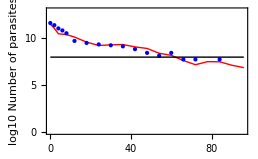

```mathematica
IDVL["mod1_1.in"]
```

## Model 1.2

Model 1.2 will do the batch run of model 1.1. The range for each parameter is from Saralamba S., et al., PNAS 2011. A set of parameters will be chosen and writen to an output file if it makes the model has RMSD < 1.0.

model | model ID
outform | output format. model 1.2 has only one format which is an output file.
parafile | the file name of the parasite count data file
concfile | the file name of DHA concentratioin data file
outname | the name of the output file (in CSV format).
runsteps | the number of parameter sets that will be put in the model

List of parameters for model 1.2.

model 1.2 will write the output to a file. The set of parameters that make the model has the RMSD < 1.0 will be written. The RMSD and the RIs for that parameter set will be written as well.

The example of the input and output of model 1.2.

model 1.2
outform 0

parafile "paraP002.csv"
concfile "P002.csv"

outname "testP002"

runsteps 5

```mathematica
IDVL["model1_2.in"]
```

******INDIVARIA*****

model: 1.2

outform: 0

********************

model: 1.2

parafile: paraP002.csv

concfile: P002.csv

runsteps: 50

outname: testP002

outform: 0

Creating an output file.

===Run no. 1===

runmax: 96

RMSD : 4.22958

The set of parameters is rejected.

===Run no. 2===

runmax: 96

RMSD : 1.20868

The set of parameters is rejected.

===Run no. 3===

runmax: 96

RMSD : 0.984853

The set of parameters is collected.

===Run no. 4===

runmax: 96

RMSD : 1.56991

The set of parameters is rejected.

===Run no. 5===

runmax: 96

RMSD : 0.892873

The set of parameters is collected.

The program is finised.

More About

List of models

Related Tutorials

Using Indivaria

Related Wolfram Education Group Courses